### Here I try to modulate a 2lvl system coupled to a classical Field

```mathematica
(*Clear all previous variables*)ClearAll["Global`*"];

(*Parameters*)
ωa=1;(*atomic energy separation*)

(*Parameters for the external, classical drive*)
ωp:=0.9 ωa; (*Freq of external drive*)
delta := ωa - ωp
E0 := 1;
mu:=1;
Ω0  :=  mu *E0 (*rabi freq*)
Ω := Sqrt[Ω0^2 + delta^2]
Tpp=2 π/Ω
Print["Tpp = ",Tpp]

time=10 Tpp;(*Total simulation time*)
interval=1000 Tpp;(*Number of time steps*)
```

6.252

Tpp = 6.252

```mathematica
g={{1},{0}};(*Ground state|g>as a column vector*)
e={{0},{1}};(*Excited state|e>as a column vector*)

(*Pauli operators*)
sz=e.Transpose[e]-g.Transpose[g];(*Pauli Z operator*)
sx=e.Transpose[g]+g.Transpose[e];(*Pauli X operator*)

(*Raising and lowering operators*)
sp=e.Transpose[g];(*Raising operator sigma+*)
sm=ConjugateTranspose[sp];(*Lowering operator sigma-*)
```

```mathematica
ElectricField[t_]:=E0 Exp[-I ωp t];(*Define ElectricField*)
```

```mathematica
(*Rabi Hamiltonian for single cavity and a classical drive*)
H[t_]=ωa e.Transpose[e]+
	Ω (ElectricField[t] + Conjugate[ElectricField[t]]) sx;

(*Drop all counter-rotating effects*)
HJC[t_]=ωa e.Transpose[e]+
Ω ElectricField[t]sm+
Ω Conjugate[ElectricField[t]]  sp;

Print[Column[{"Rabi Hamiltonian:",                                   Row[{"H[t_] = ",TraditionalForm[H[t]]}],
"Hamiltonian with counter-rotating effects:", Row[{"HJC[t_] = ",TraditionalForm[HJC[t]]}] }]];
```

Rabi Hamiltonian:
H[t_] = (0. | 1.00499 cos(0.9 t)
1.00499 cos(0.9 t) | 1.)
Hamiltonian with counter-rotating effects:
HJC[t_] = (0. | 0.+0.502494 ⅇ^((0.-0.9 ⅈ) t)
0.+0.502494 ⅇ^((0.+0.9 ⅈ) t) | 1.)

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

NDSolveValue::underdet: There are more dependent variables, {ψ1[t],ψ2[t]}, than equations, so the system is underdetermined.

NDSolveValue::dsvar: 0. cannot be used as a variable.

NDSolveValue::dsvar: 0.01 cannot be used as a variable.

NDSolveValue::dsvar: 0.02 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NDSolveValue::dsvar: 0. cannot be used as a variable.

Part::partw: Part 2 of NDSolveValue[{{ⅈ ψ1'[0.],ⅈ ψ2'[0.]}==HJC.{ψ1[0.],ψ2[0.]},{ψ1[0],ψ2[0]}=={{1},{0}}},ψ,{0.,0,62.52}][0.] does not exist.

NDSolveValue::dsvar: 0.01 cannot be used as a variable.

Part::partw: Part 2 of NDSolveValue[{{ⅈ ψ1'[0.01],ⅈ ψ2'[0.01]}==HJC.{ψ1[0.01],ψ2[0.01]},{ψ1[0],ψ2[0]}=={{1},{0}}},ψ,{0.01,0,62.52}][0.01] does not exist.

NDSolveValue::dsvar: 0.02 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

Part::partw: Part 2 of NDSolveValue[{{ⅈ ψ1'[0.02],ⅈ ψ2'[0.02]}==HJC.{ψ1[0.02],ψ2[0.02]},{ψ1[0],ψ2[0]}=={{1},{0}}},ψ,{0.02,0,62.52}][0.02] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolveValue::dsvar: 0. cannot be used as a variable.

Part::partw: Part 2 of NDSolveValue[{{1. ⅈ ψ1'[0.],1. ⅈ ψ2'[0.]}==HJC.{ψ1[0.],ψ2[0.]},{ψ1[0],ψ2[0]}=={{1.},{0}}},ψ,{0.,0,62.52}][0.] does not exist.

NDSolveValue::dsvar: 0.01 cannot be used as a variable.

Part::partw: Part 2 of NDSolveValue[{{1. ⅈ ψ1'[0.01],1. ⅈ ψ2'[0.01]}==HJC.{ψ1[0.01],ψ2[0.01]},{ψ1[0],ψ2[0]}=={{1.},{0}}},ψ,{0.01,0,62.52}][0.01] does not exist.

NDSolveValue::dsvar: 0.02 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

Part::partw: Part 2 of NDSolveValue[{{1. ⅈ ψ1'[0.02],1. ⅈ ψ2'[0.02]}==HJC.{ψ1[0.02],ψ2[0.02]},{ψ1[0],ψ2[0]}=={{1.},{0}}},ψ,{0.02,0,62.52}][0.02] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Callout::copos: {Automatic} is not a valid position for the placement of callouts.

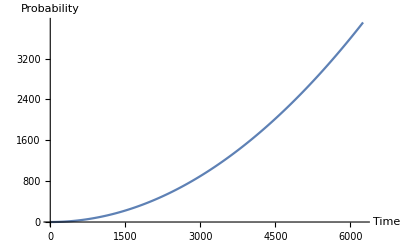

-Graphics-

```mathematica
ψ[t_]={ψ1[t],ψ2[t]};(*Define ψ[t] as a vector*)

sol=NDSolveValue[{I ψ'[t]==HJC.ψ[t],ψ[0]==g},ψ,{t,0,time}];
(*sol=NDSolveValue[{I ψ'[t]==H.ψ[t],ψ[0]==g},ψ,{t,0,time}];*)

groundStateProbabilities=Table[Abs[sol[t][[1]]]^2,{t,0,time,time/interval}];
excitedStateProbabilities=Table[Abs[sol[t][[2]]]^2,{t,0,time,time/interval}];

ListLinePlot[{groundStateProbabilities,excitedStateProbabilities},
PlotRange->All,PlotLabels->{"Ground State","Excited State"},
AxesLabel->{"Time","Probability"},
PlotLegends->"Expressions"
]
```